NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.7912×10^14}. NIntegrate obtained 0.00126466 and 0.000110768 for the integral and error estimates.

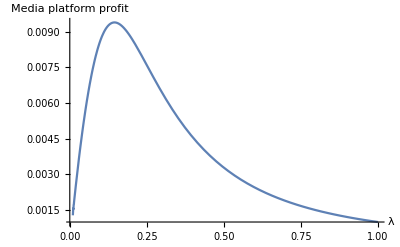

```mathematica
ClearAll[r,cond1,cond2,cond3,cond4,Pif,PiI,MI,optimize];
r[λ_?NumericQ]:=Exp[-1/λ];
P1=0.1;
P2=0.2;
cond1U[x_?NumericQ,w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=0<x<λ*Log[2/(Exp[-1/λ]+1)]-w-p1;
cond2U[x_?NumericQ, w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=λ*Log[2/(Exp[-1/λ]+1)]-w-p1<x<-λ Log[2/(Exp[1/λ]+1)]-w-p1;
cond3U[x_?NumericQ,w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=1>x>-λ Log[2/(Exp[1/λ]+1)]-w-p1;
cond4U[w_?NumericQ,λ_?NumericQ]:=λ<0.01;

cond1[w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=2/(r[λ]+1)>=Exp[(w+p1)/λ];
cond2[w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=2/(r[λ]+1)<Exp[(w+p1)/λ]<=(r[λ]+1)/(2 r[λ]);
cond3[w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=Exp[(w+p1)/λ]>(r[λ]+1)/(2 r[λ]);
cond4[w_?NumericQ,λ_?NumericQ]:=λ<0.01;


MI[x_?NumericQ,w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=1/2*((Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x)) Log[2]+(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)Log[(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)]+(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)Log[(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)]-(Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x))Log[(Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x))]+(x Exp[-1/λ]^2-2 Exp[-1/λ]+Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)Log[(x Exp[-1/λ]^2-2 Exp[-1/λ]+Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)]+(Exp[-1/λ] x+x-2)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)Log[(Exp[-1/λ] x+x-2)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)]-(2-(Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x)))Log[1-1/2 (Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x))]);

PiI[w_?NumericQ,λ_?NumericQ,p1_?NumericQ,p2_?NumericQ]:=Piecewise[{{0,cond3[w,λ,p1]},{0,cond4[w,λ]},
{NIntegrate[p2*MI[x,w,λ,p1] λ^2/x,{x,2/(Exp[-1/λ]+1),(Exp[-1/λ]+1)/(2 Exp[-1/λ])}],cond1[w,λ,p1]},{NIntegrate[p2*MI[x,w,λ,p1] λ^2/x,{x,Exp[(w+p1)/λ],(Exp[-1/λ]+1)/(2 Exp[-1/λ])}],cond2[w,λ,p1]}}];

Plot[PiI[0,λ,0,P2],{λ,0.01,1},AxesLabel->{"λ","Media platform profit"}, PlotRange->All]
```

```mathematica
Pif[w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=Piecewise[{
{0,cond3[w,λ,p1]},
{w*p1*(1-w-p1)/2,cond4[w,λ]},
{p1*w*(1/2-w-p1),cond1[w,λ,p1]},
{(p1*w*λ/2)*(Log[((r[λ]+1)/(2*r[λ])-1)/(Exp[(w+p1)/λ]-1)]+Log[(r[λ]*((r[λ]+1)/(2*r[λ]))-1)/(r[λ]*Exp[(w+p1)/λ]-1)]),cond2[w,λ,p1]}
}];

resp=FindMaximum[Pif[w,0.005,P1],{w,0.1}];
resm=FindMaximum[PiI[0,λ,0,P2],{λ,0.1}];


λm=λ/. resm[[2]]

wp=w/. resp[[2]]
```

0.145052

0.45

```mathematica
MI[x_?NumericQ,w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=1/2*((Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1]) (1/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)+1/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])) Log[2]+(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1])/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)Log[(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1])/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)]+(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1])/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])Log[(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1])/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])]-(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1]) (1/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)+1/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1]))Log[(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1]) (1/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)+1/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1]))]+(B[x,w,λ,p1] Exp[-1/λ]^2-2 Exp[-1/λ]+Exp[-1/λ] B[x,w,λ,p1])/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)Log[(B[x,w,λ,p1] Exp[-1/λ]^2-2 Exp[-1/λ]+Exp[-1/λ] B[x,w,λ,p1])/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)]+(Exp[-1/λ] B[x,w,λ,p1]+B[x,w,λ,p1]-2)/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])Log[(Exp[-1/λ] B[x,w,λ,p1]+B[x,w,λ,p1]-2)/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])]-(2-(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1]) (1/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)+1/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])))Log[1-1/2 (Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1]) (1/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)+1/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1]))]);

B[x_?NumericQ,w_?NumericQ,λ_?NumericQ,p1_?NumericQ]=Exp[(x+w+p1)/λ];
H[x_?NumericQ,w_?NumericQ,λ_?NumericQ,p1_?NumericQ]=(r[λ]+1-2r[λ]B[x,w,λ,p1])/(B[x,w,λ,p1]r[λ]^2-r[λ]-r[λ]B[x,w,λ,p1]+1);
L[x_?NumericQ,w_?NumericQ,λ_?NumericQ,p1_?NumericQ]=(r[λ]+1-2r[λ]B[x,w,λ,p1])/(r[λ]+B[x,w,λ,p1]-r[λ]B[x,w,λ,p1]-1);
U[x_?NumericQ,w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=Piecewise[{
{0.5-w-p1,cond1U[x,w,λ,p1]},
{0.5(H[x,w,λ,p1]*(1-w-p1)+L[x,w,λ,p1]*(-w-p1)+(2-H[x,w,λ,p1]-L[x,w,λ,p1])*x)-λ*MI[x,w,λ,p1],cond2U[x,w,λ,p1]},
{x,cond3U[x,w,λ,p1]}
}];

Plot[{U[x,0,λm,0],U[x,wp,0.01,P1],x, Max[x,(1+x)/2],U[x,0.2,0.13,P1]},{x,0,1}, PlotRange->{0,1},PlotStyle->{Blue,Green,{Black,Dashed,Opacity[0.6]}, {Black,Dotted,Opacity[0.6]},{Red}},AxesLabel->{"ε","E[U[ε]]"}]
```

```mathematica
MI[x_?NumericQ,w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=1/2*((Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x)) Log[2]+(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)Log[(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)]+(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)Log[(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)]-(Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x))Log[(Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x))]+(x Exp[-1/λ]^2-2 Exp[-1/λ]+Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)Log[(x Exp[-1/λ]^2-2 Exp[-1/λ]+Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)]+(Exp[-1/λ] x+x-2)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)Log[(Exp[-1/λ] x+x-2)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)]-(2-(Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x)))Log[1-1/2 (Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x))]);

PiI[w_?NumericQ,λ_?NumericQ,p1_?NumericQ,p2_?NumericQ]:=Piecewise[{{0,cond3[w,λ,p1]},{0,cond4[w,λ]},
{NIntegrate[p2*MI[x,w,λ,p1] λ^2/x,{x,2/(Exp[-1/λ]+1),(Exp[-1/λ]+1)/(2 Exp[-1/λ])}],cond1[w,λ,p1]},{NIntegrate[p2*MI[x,w,λ,p1] λ^2/x,{x,Exp[(w+p1)/λ],(Exp[-1/λ]+1)/(2 Exp[-1/λ])}],cond2[w,λ,p1]}}];

cond1[w_,λ_,p1_]:=2/(r[λ]+1)>=Exp[(w+p1)/λ];
cond2[w_,λ_,p1_]:=2/(r[λ]+1)<Exp[(w+p1)/λ]<=(r[λ]+1)/(2 r[λ]);
cond3[w_,λ_,p1_]:=Exp[(w+p1)/λ]>(r[λ]+1)/(2 r[λ]);
cond4[w_,λ_]:=λ<0.01;

Pifg[w_,λ_,p1_]:=Piecewise[{
{0,cond3[w,λ,p1]},
{w*p1*(1-w-p1)/2,cond4[w,λ]},
{p1*w*(1/2-w-p1),cond1[w,λ,p1]},
{(p1*w*λ/2)*(Log[((r[λ]+1)/(2*r[λ])-1)/(Exp[(w+p1)/λ]-1)]+Log[(r[λ]*((r[λ]+1)/(2*r[λ]))-1)/(r[λ]*Exp[(w+p1)/λ]-1)]),cond2[w,λ,p1]}
}];

MIg[λ_,x_]:=1/2*((Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x)) Log[2]+(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)Log[(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)]+(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)Log[(Exp[-1/λ]+1-2 Exp[-1/λ] x)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)]-(Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x))Log[(Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x))]+(x Exp[-1/λ]^2-2 Exp[-1/λ]+Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)Log[(x Exp[-1/λ]^2-2 Exp[-1/λ]+Exp[-1/λ] x)/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)]+(Exp[-1/λ] x+x-2)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)Log[(Exp[-1/λ] x+x-2)/(Exp[-1/λ]-Exp[-1/λ] x-1+x)]-(2-(Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x)))Log[1-1/2 (Exp[-1/λ]+1-2 Exp[-1/λ] x) (1/(x Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] x+1)+1/(Exp[-1/λ]-Exp[-1/λ] x-1+x))]);

PiIg[w_?NumericQ,λ_?NumericQ,p1_,p2_]:=Piecewise[{{0,cond3[w,λ,p1]},{0,cond4[w,λ]},
{NIntegrate[p2*MIg[λ,x] λ^2/x,{x,2/(Exp[-1/λ]+1),(Exp[-1/λ]+1)/(2 Exp[-1/λ])}],cond1[w,λ,p1]},{NIntegrate[p2*MIg[λ,x] λ^2/x,{x,Exp[(w+p1)/λ],(Exp[-1/λ]+1)/(2 Exp[-1/λ])}],cond2[w,λ,p1]}}];
(*Pif*)maxPif=NMaximize[{Pif[w,λ,0.1],0.01<=w<=1&&0<=λ<=1},{w,λ}];


resg=FindMaximum[Pifg[w,λ,P1]+PiIg[w,λ,P1,P2],{{λ,0.1},{w,0.1}}];

{λstar,wstar}={λ,w}/. resg[[2]];
Pif[w_?NumericQ,λ__?NumericQ,p1_?NumericQ]:=Piecewise[{
{0,cond3[w,λ,p1]},
{w*p1*(1-w-p1)/2,cond4[w,λ]},
{p1*w*(1/2-w-p1),cond1[w,λ,p1]},
{(p1*w*λ/2)*(Log[((r[λ]+1)/(2*r[λ])-1)/(Exp[(w+p1)/λ]-1)]+Log[(r[λ]*((r[λ]+1)/(2*r[λ]))-1)/(r[λ]*Exp[(w+p1)/λ]-1)]),cond2[w,λ,p1]}
}];

resp=FindMaximum[Pif[w,0.005,P1],{w,0.1}];
resm=FindMaximum[PiI[0,λ,0,P2],{λ,0.1}];


λm=λ/. resm[[2]];

wp=w/. resp[[2]];


Pif[wp,0.005,P1]
PiI[0,λm,0,P2]
Pifg[λstar,wstar,P1]+ PiIg[λstar,wstar,P1,P2]


P1=0.1;
P2=0.4;


f1[P1_?NumericQ,P2_?NumericQ]:=Pif[wp,0.005,P1];

f2[P1_?NumericQ,P2_?NumericQ]:=PiI[0,λm,0,P2];

f3[P1_?NumericQ,P2_?NumericQ]:=Pifg[λstar,wstar,P1]+PiIg[λstar,wstar,P1,P2];

P1min=0.01;P1max=0.5;
P2min=0.01;P2max=0.5;

(*ContourPlot[f1[P1,P2],{P1,P1min,P1max},{P2,P2min,P2max},Contours->15,FrameLabel->{"P1","P2"}]
ContourPlot[f2[P1,P2],{P1,P1min,P1max},{P2,P2min,P2max},Contours->15,FrameLabel->{"P1","P2"}]
ContourPlot[f3[P1,P2],{P1,P1min,P1max},{P2,P2min,P2max},Contours->15,FrameLabel->{"P1","P2"}]*)

winner[P1_?NumericQ,P2_?NumericQ]:=Module[{v1,v2,v3},{v1,v2,v3}={f1[P1,P2],f2[P1,P2],f3[P1,P2]};
First@Ordering[{v1,v2,v3},-1]]
```

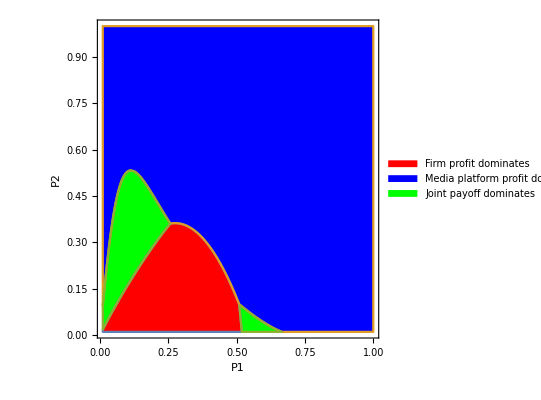

```mathematica
RegionPlot[{winner[P1,P2]==1,winner[P1,P2]==2,winner[P1,P2]==3},{P1,0.01,1},{P2,0.01,1},PlotStyle->{Red,Blue,Green},FrameLabel->{"P1","P2"},PlotLegends->{"Firm profit dominates","Media platform profit dominates","Joint payoff dominates"},PlotPoints->40,MaxRecursion->2]
```

```mathematica
ContourPlot[{f1[P1,P2]-f2[P1,P2],f1[P1,P2]-f3[P1,P2],f2[P1,P2]-f3[P1,P2]},{P1,0.01,1},{P2,0.01,1},Contours->{0},ContourStyle->{Red,Blue,Green},FrameLabel->{"P1","P2"}]
```

0.010125

0.00939875

0.0117395

$Aborted

-Graphics-

FindMaximum::nrnum: The function value -PiI[1.,2.] is not a real number at {λ} = {1.}.

ReplaceAll::reps: {λ,1.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

λ/.{λ,1.}

FindMaximum::nrnum: The function value -(Piecewise[{{0, cond3[0.1,0.1,0.1]}, {0.003, cond1[0.1,0.1,0.1]}, {0.00337968, cond2[0.1,0.1,0.1]}, {0, True}}]) is not a real number at {λ,w} = {0.1,0.1}.

ReplaceAll::reps: {λ,0.1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {w,0.1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{λ,w}/.{λ,0.1},{λ,w}/.{w,0.1}}